## Lab 4

Using graph and table, estimate the limit of 1/x as x approaches positive infinity.

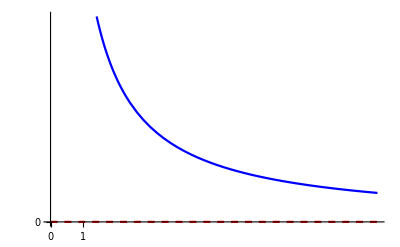

x | 1/x
-100000 | -0.00001
-90000 | -0.000011111111
-80000 | -0.0000125
-70000 | -0.000014285714
-60000 | -0.000016666667
-50000 | -0.00002
-40000 | -0.000025
-30000 | -0.000033333333
-20000 | -0.00005
-10000 | -0.0001 | x | 1/x
-10000 | -0.0001
-9000 | -0.00011111111
-8000 | -0.000125
-7000 | -0.00014285714
-6000 | -0.00016666667
-5000 | -0.0002
-4000 | -0.00025
-3000 | -0.00033333333
-2000 | -0.0005
-1000 | -0.001 | x | 1/x
1000 | 0.001
2000 | 0.0005
3000 | 0.00033333333
4000 | 0.00025
5000 | 0.0002
6000 | 0.00016666667
7000 | 0.00014285714
8000 | 0.000125
9000 | 0.00011111111
10000 | 0.0001 | x | 1/x
10000 | 0.0001
20000 | 0.00005
30000 | 0.000033333333
40000 | 0.000025
50000 | 0.00002
60000 | 0.000016666667
70000 | 0.000014285714
80000 | 0.0000125
90000 | 0.000011111111
100000 | 0.00001

```mathematica
Clear[x]
g[x_]:= 1/x
f[x_]:=N[g[x],8]
Plot[{0,f[x]},{x,0,10}, PlotRange->Automatic, PlotStyle->{{Red, Dashed},{Blue}},Ticks->{{-1,0,1},{0,1,2}}]
Grid[{
Map[TableForm,{
Join[{{x,g[x]}},Table[{x,f[x]},{x,-100000,-10000,10000}]],(* each Table here has the same size *)
Join[{{x,g[x]}},Table[{x,f[x]},{x,-10000,-1000,1000}]],
Join[{{x,g[x]}},Table[{x,f[x]},{x,1000,10000,1000}]],
Join[{{x,g[x]}},Table[{x,f[x]},{x,10000,100000,10000}]]
}]
},Spacings->3]
```

The table indicates that f(x) approaches 0 as x goes to infinity.

Using graph and table, estimate the limit of 1/x as x approaches negative infinity.

```mathematica
g[x_]:= 1/x
f[x_]:=N[g[x],8]
Plot[{0,f[x]},{x,0,10}, PlotRange->Automatic, PlotStyle->{{Red, Dashed},{Blue}},Ticks->{{-1,0,1},{0,1,2}}]
Grid[{
Map[TableForm,{
Join[{{x,g[x]}},Table[{x,f[x]},{x,-100000,-10000,10000}]],(* each Table here has the same size *)
Join[{{x,g[x]}},Table[{x,f[x]},{x,-10000,-1000,1000}]],
Join[{{x,g[x]}},Table[{x,f[x]},{x,1000,10000,1000}]],
Join[{{x,g[x]}},Table[{x,f[x]},{x,10000,100000,10000}]]
}]
},Spacings->3]
```

-Graphics-

x | 1/x
-100000 | -0.00001
-90000 | -0.000011111111
-80000 | -0.0000125
-70000 | -0.000014285714
-60000 | -0.000016666667
-50000 | -0.00002
-40000 | -0.000025
-30000 | -0.000033333333
-20000 | -0.00005
-10000 | -0.0001 | x | 1/x
-10000 | -0.0001
-9000 | -0.00011111111
-8000 | -0.000125
-7000 | -0.00014285714
-6000 | -0.00016666667
-5000 | -0.0002
-4000 | -0.00025
-3000 | -0.00033333333
-2000 | -0.0005
-1000 | -0.001 | x | 1/x
1000 | 0.001
2000 | 0.0005
3000 | 0.00033333333
4000 | 0.00025
5000 | 0.0002
6000 | 0.00016666667
7000 | 0.00014285714
8000 | 0.000125
9000 | 0.00011111111
10000 | 0.0001 | x | 1/x
10000 | 0.0001
20000 | 0.00005
30000 | 0.000033333333
40000 | 0.000025
50000 | 0.00002
60000 | 0.000016666667
70000 | 0.000014285714
80000 | 0.0000125
90000 | 0.000011111111
100000 | 0.00001

The table indicates that f(x) approaches 0 as x goes to negative infinity.

Using graph, estimate the limit of 1/x as x approaches 0. Does it exist? What are the two one-sided limits?

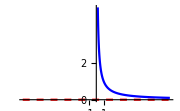

x | 1/x
-1.1 | -0.909091
-0.9 | -1.11111
-0.7 | -1.42857
-0.5 | -2.
-0.3 | -3.33333
-0.1 | -10.
0.1 | 10.
0.3 | 3.33333
0.5 | 2.
0.7 | 1.42857
0.9 | 1.11111
1.1 | 0.909091 | x | 1/x
-0.11 | -9.09091
-0.09 | -11.1111
-0.07 | -14.2857
-0.05 | -20.
-0.03 | -33.3333
-0.01 | -100.
0.01 | 100.
0.03 | 33.3333
0.05 | 20.
0.07 | 14.2857
0.09 | 11.1111
0.11 | 9.09091 | x | 1/x
-0.011 | -90.9091
-0.009 | -111.111
-0.007 | -142.857
-0.005 | -200.
-0.003 | -333.333
-0.001 | -1000.
0.001 | 1000.
0.003 | 333.333
0.005 | 200.
0.007 | 142.857
0.009 | 111.111
0.011 | 90.9091

```mathematica
Clear[x]
g[x_]:=1/x
f[x_]:=N[g[x],8]
Plot[{0,f[x]},{x,-10,10},PlotRange->{0,5},PlotStyle->{{Red, Dashed},{Blue}},Ticks->{{-1,0,1},{0,1,2}},ImageSize->180]
Grid[{
Map[TableForm,{
Join[{{x,g[x]}},Table[{x,f[x]},{x,-1.1,1.1,0.2}]],
Join[{{x,g[x]}},Table[{x,f[x]},{x,-0.11,0.11,0.02}]],
Join[{{x,g[x]}},Table[{x,f[x]},{x,-0.011,0.011,0.002}]]
}]
},Spacings->3]
```

The table indicates that the limit of 1/x as x approaches 0 does not exist. As it approaches zero from the right, the limit is infinity. As it approaches zero from the left, the limit is negative infinity.

Using the built-in function Limit, find each limit.

limit_(x→1^+)x/(x-1)

```mathematica
Limit[x/(x-1),x-> -1]
```

1/2

limit_(x→1)(x^2+4x-5)/(x-1)

```mathematica
Limit[(x^2+4x-5)/(x-1),x-> 1]
```

6

limit_(x→0)x/(sin x)

```mathematica
Limit[x/Sin[x],x->0]
```

1

limit_(x→∞)(1+x)^(1/x)

```mathematica
Limit[(1+x)^(1/x),x-> ∞]
```

1

limit_(x→∞) x^10/ⅇ^x

```mathematica
Limit[x^10/ⅇ^x,x-> ∞]
```

0

limit_(x→+∞) (ln x)/x

```mathematica
Limit[Log[x]/x,x->∞]
```

0

limit_(x→0^+) (ln x)/x^2

```mathematica
Limit[Log[x]/x^2,x-> -0]
```

-∞

limit_(x→0^+) x^5 ln x

```mathematica
Limit[x^5*Log[x],x->-0]
```

0

Plot each function and find its asymptotes if there are any. Then, use Limit to confirm your conclusions.

f(x)=ⅇ^x

```mathematica
f[x_]:=ⅇ^x
{Limit[f[x],x->∞],Limit[f[x],x->-∞]}
```

{∞,0}

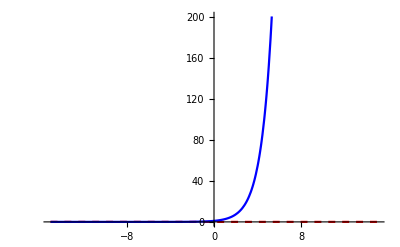

```mathematica
Plot[{0,f[x]},{x,-15,15},PlotStyle->{{Red,Dashed},{Blue}},PlotRange->Automatic]
```

g(x)=e^(1/x)

```mathematica
Clear[x]
```

```mathematica
g[x_]:=ⅇ^(1/x)
{Limit[g[x],x->∞],Limit[g[x],x->-∞]}
```

{1,1}

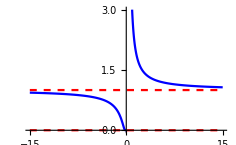

```mathematica
Plot[{1,0,g[x]},{x,-15,15},PlotStyle->{{Red,Dashed},{Red,Dashed},{Blue}},PlotRange->{0,3}]
```

h(x)=(x+3)/(x^2-3x-4)

```mathematica
h[x_]:=(x+3)/(x^2-3x-4)
{Limit[h[x],x->∞],Limit[h[x],x->-∞]}
```

{0,0}

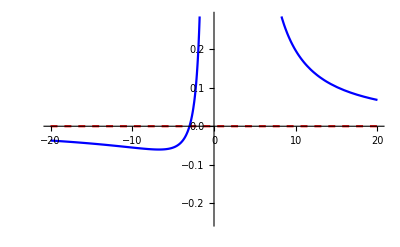

```mathematica
Plot[{0,h[x]},{x,-20,20},PlotStyle->{{Red,Dashed},{Blue}},PlotRange->Automatic]
```

k(x)=(3 x^2-5x+1)/(x^2+2x-8)

```mathematica
k[x_]:=(3 x^2-5x+1)/(x^2+2x-8)
{Limit[k[x],x->∞],Limit[k[x],x->-∞]}
```

{3,3}

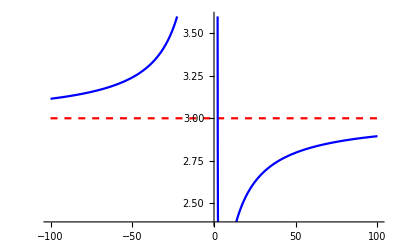

```mathematica
Plot[{3,k[x]},{x,-100,100},PlotStyle->{{Red,Dashed},{Blue}},PlotRange->Automatic]
```

m(x)=sin x

```mathematica
m[x_]:=Sin[x]
{Limit[m[x],x->∞],Limit[m[x],x->-∞]}
```

{Indeterminate,Indeterminate}

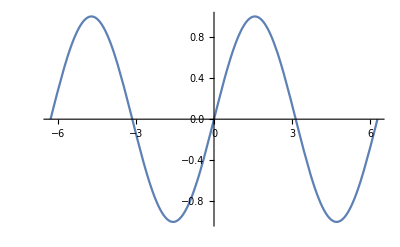

```mathematica
Plot[{Sin[x]},{x,-2Pi,2Pi}]
```

By definition, finding the derivatives of each function at specified points.

f(x)=x^2 ⅇ^x,x=1,2

```mathematica
f[x_]:=x^2 ⅇ^x
Limit[(f[x+h]-f[x])/h,h->0]
```

```mathematica
ⅇ^x x (2+x)
%/.x->1
```

ⅇ^x x (2+x)

3 ⅇ

```mathematica
%/.x->2
```

3 ⅇ

g(x)=(sin x)/x+3x cos x,x=π/4,π/2

```mathematica
g[x_]:=Sin[x]/x+3x*Cos[x]
Limit[(g[x+h]-g[x])/h,h->0]
```

(3+1/x) Cos[x]-((1+3 x^3) Sin[x])/x^2

```mathematica
%/.x->π/4
```

(3+4/π)/(√2)-(8 √2 (1+(3 π^3)/64))/π^2

```mathematica
%/.x->π/2
```

(3+4/π)/(√2)-(8 √2 (1+(3 π^3)/64))/π^2

Referring to the last section, Graphics objects and operations, and the following example, plot each of the four functions, f(x)=ⅇ^x, g(x)=e^(1/x), h(x)=(x+3)/(x^2-3x-4), and m(x)=sin x, with its expression, such as sin x, displayed near the curve, choose one point on the curve and mark it with a red point, and present all graphs on a 2×2 grid.

```mathematica
GraphicsGrid[
Show[{
Plot[ⅇ^x,{x,-3,3},ImageSize->180],
Graphics[{Red,Text[Style["e^x",Italic,Bold],{1,5}]}],
Graphics[{Red,PointSize[Medium],Point[{1,ⅇ^1}]}]
}]
Show[{
Plot[ⅇ^(1/x),{x,-5,5},ImageSize->180],
Graphics[{Red,Text[Style["e^(1/x)",Italic,Bold],{2,3}]}],
Graphics[{Red,PointSize[Medium],Point[{2,ⅇ^(1/2)}]}]
}]
Show[{
Plot[(x+3)/(x^2-3x-4),{x,-3,3},ImageSize->180],
Graphics[{Red,Text[Style["x + 3",Italic,Bold],{1,1}]}],
Graphics[{Red,PointSize[Medium],Point[{1,(-2/3)}]}]
}]
Show[{
Plot[Sin[x],{x,-3,3},ImageSize->180],
Graphics[{Red,Text[Style["sin(x)",Italic,Bold],{1,1}]}],
Graphics[{Red,PointSize[Medium],Point[{1,Sin[1]}]}]
}]]
```

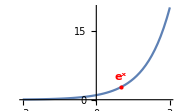
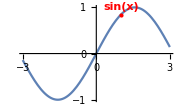
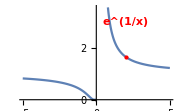
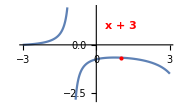
```mathematica
-Graphics- -Graphics- -Graphics- -Graphics-]
```